```mathematica
G[x_] = Exp[-x^2/2]
```

ⅇ^(-x^2/2)

```mathematica
F[x_,y_] = ρ[x]/ Abs[x-y]
```

(ⅇ^(-x^2/2))/Abs[x-y]

```mathematica
(ⅇ^x (-1+x^2))/Abs[x-0.1]
```

```mathematica
Table[NIntegrate[F[x,y],{x,-10,10}],{y,-10,10,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-5.4999999999999999999999999997472374027688857002385405809275507253}. NIntegrate obtained 0.472684 and 6.79176×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-5.3999999999999692688928903924975722464857668883360684647029770211}. NIntegrate obtained 0.48213 and 0.0000202002 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-5.3000000000000093097655397087754171359474663059065447138183679865}. NIntegrate obtained 0.492084 and 4.65781×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
xaxis={0.25324870441783637,0.2558615580331234,0.25852951612365116,0.2612543619876839,0.2640379577218525,0.26688224868318544,0.26978926826238103,0.2727611429943609,0.2758000980347033,0.27890846303341865,0.28208867844071817,0.2853433022829401,0.2886750174507437,0.2920866395472562,0.295581125345306,0.2991615819143484,0.3028312764786022,0.3065936470781916,0.31045231411232316,0.314411092852945,0.31847400702789885,0.3226453035846915,0.3269294687591219,0.33133124559179084,0.335855653048593,0.3405080069221949,0.345293942732159,0.35021944083840667,0.35529085404636235,0.36051493800396656,0.3658988847420038,0.3714503597632226,0.3771775431513306,0.3830891752502934,0.3891946075674555,0.39550385962488144,0.4020276828048022,0.4087776320825343,0.4157661472137882,0.42300663915857856,0.4305136242068876,0.4383027874718286,0.4463911808085696,0.4547973579617898,0.46354619765161154,0.4726841026487511,0.48212989839177134,0.4920839009689188,0.5025674201340774,0.5133270118105199,0.5250500841737135,0.5364611123263321,0.5494900666144797,0.5638228021544778,0.5766233983716027,0.5963012831873806,0.6140755961376854,0.625375230205689,0.661492807503534,0.665526875110223,0.7277502902349959,0.7654528835067169,0.7453523631999663,0.8736662807732912,0.8289006123485145,1.124488664506452,1.2466584685124174,0.9917924040944225,1.7906213194105152,2.059009956289438,2.6375756601445657,3.087032354962471,1.5754111168473557,3.151588504721599,7.340007436037553,9.58122597742856,10.329053485334471,1.1253819621461152,31.279171890005536,13.100052503252448,21.91356935186799,22.77749914963296,14.620358274349321,16.57973344257835,43.47540906841239,50.525245125193486,58.178138605040154,57.09695761460164,74.98982403383943,68.8499544866466,92.61226994653711,86.97902571690898,49.6559183962751,51.61761761985272,126.85796273014368,133.92203646066167,139.99634846162968,67.65645534043617,148.5304319589065,63.64067179136951,191614.20706662888,131.12116379160278,137.4387281952101,122.26910499303402,139.99634846162957,133.9220364606617,126.85796273014356,103.63224461349475,110.52802087053094,86.97902571690898,92.61226994653711,40.68775715192189,39.38096922521411,29.961692443480082,58.178138605040154,50.525245125193486,43.47540906841227,32.549485769605774,31.33194284046635,22.777499149632966,21.91356935186799,11.686328955862916,5.917795798470138,6.861880497079784,11.459683682709226,9.58122597742856,7.340007436037526,4.587963756417152,4.701710610985005,1.776137703090147,2.6375756601445657,1.5871724293134544,1.1729056224850007,1.1460659160863989,0.9544542244056964,1.124488664506452,0.9992170937899091,0.8349170740269871,0.8307634167931401,0.7192365544752606,0.7277502902349959,0.6664625984373,0.6478378697449606,0.628461118362213,0.6090658497413968,0.5963012831873807,0.5795394865781485,0.5627612157635407,0.5502978602844635,0.5364611123263321,0.5250500841737133,0.5134509392714968,0.5025345125905835,0.49213093667207125,0.48212989839177134,0.47268410264875116,0.46356343891597396,0.4547973579617897,0.4463911808085696,0.43830278747182877,0.4305136242068876,0.42300663915857845,0.4157661472137882,0.40877763208253437,0.4020276828048021,0.3955038596248815,0.3891946075674554,0.3830891752502934,0.3771775431513307,0.3714503597632225,0.3658988847420038,0.3605149380039666,0.3552908540463624,0.35021944083840667,0.3452939427321589,0.34050800692219496,0.335855653048593,0.33133124559179084,0.3269294687591219,0.3226453035846914,0.3184740070278989,0.314411092852945,0.31045231411232316,0.3065936470781916,0.3028312764786022,0.2991615819143485,0.29558112534530595,0.29208663954725617,0.2886750174507437,0.2853433022829402,0.282088678440718,0.2789084630334187,0.27580009803470323,0.27276114299436083,0.2697892682623809,0.2668822486831854,0.26403795772185246,0.2612543619876838,0.25852951612365116,0.25586155803312327,0.2532487044178363}
```

{0.253249,0.255862,0.25853,0.261254,0.264038,0.266882,0.269789,0.272761,0.2758,0.278908,0.282089,0.285343,0.288675,0.292087,0.295581,0.299162,0.302831,0.306594,0.310452,0.314411,0.318474,0.322645,0.326929,0.331331,0.335856,0.340508,0.345294,0.350219,0.355291,0.360515,0.365899,0.37145,0.377178,0.383089,0.389195,0.395504,0.402028,0.408778,0.415766,0.423007,0.430514,0.438303,0.446391,0.454797,0.463546,0.472684,0.48213,0.492084,0.502567,0.513327,0.52505,0.536461,0.54949,0.563823,0.576623,0.596301,0.614076,0.625375,0.661493,0.665527,0.72775,0.765453,0.745352,0.873666,0.828901,1.12449,1.24666,0.991792,1.79062,2.05901,2.63758,3.08703,1.57541,3.15159,7.34001,9.58123,10.3291,1.12538,31.2792,13.1001,21.9136,22.7775,14.6204,16.5797,43.4754,50.5252,58.1781,57.097,74.9898,68.85,92.6123,86.979,49.6559,51.6176,126.858,133.922,139.996,67.6565,148.53,63.6407,191614.,131.121,137.439,122.269,139.996,133.922,126.858,103.632,110.528,86.979,92.6123,40.6878,39.381,29.9617,58.1781,50.5252,43.4754,32.5495,31.3319,22.7775,21.9136,11.6863,5.9178,6.86188,11.4597,9.58123,7.34001,4.58796,4.70171,1.77614,2.63758,1.58717,1.17291,1.14607,0.954454,1.12449,0.999217,0.834917,0.830763,0.719237,0.72775,0.666463,0.647838,0.628461,0.609066,0.596301,0.579539,0.562761,0.550298,0.536461,0.52505,0.513451,0.502535,0.492131,0.48213,0.472684,0.463563,0.454797,0.446391,0.438303,0.430514,0.423007,0.415766,0.408778,0.402028,0.395504,0.389195,0.383089,0.377178,0.37145,0.365899,0.360515,0.355291,0.350219,0.345294,0.340508,0.335856,0.331331,0.326929,0.322645,0.318474,0.314411,0.310452,0.306594,0.302831,0.299162,0.295581,0.292087,0.288675,0.285343,0.282089,0.278908,0.2758,0.272761,0.269789,0.266882,0.264038,0.261254,0.25853,0.255862,0.253249}

```mathematica
yaxis=Table[G[x] ,{x,-10,10,0.1}]
```

{1.92875×10^-22,5.21674×10^-22,1.39694×10^-21,3.70353×10^-21,9.72099×10^-21,2.52616×10^-20,6.49935×10^-20,1.65552×10^-19,4.17501×10^-19,1.04241×10^-18,2.57676×10^-18,6.30619×10^-18,1.52798×10^-17,3.66543×10^-17,8.70543×10^-17,2.04697×10^-16,4.7653×10^-16,1.09831×10^-15,2.50622×10^-15,5.662×10^-15,1.26642×10^-14,2.8044×10^-14,6.1484×10^-14,1.33457×10^-13,2.86798×10^-13,6.10194×10^-13,1.28534×10^-12,2.68055×10^-12,5.53461×10^-12,1.13138×10^-11,2.28973×10^-11,4.58796×10^-11,9.10147×10^-11,1.78756×10^-10,3.47589×10^-10,6.69159×10^-10,1.27541×10^-9,2.40672×10^-9,4.49635×10^-9,8.3167×10^-9,1.523×10^-8,2.76124×10^-8,4.95641×10^-8,8.80818×10^-8,1.54975×10^-7,2.69958×10^-7,4.65572×10^-7,7.94939×10^-7,1.34381×10^-6,2.24906×10^-6,3.72665×10^-6,6.11357×10^-6,9.9295×10^-6,0.0000159668,0.0000254193,0.0000400653,0.0000625215,0.0000965934,0.000147748,0.000223746,0.000335463,0.000497955,0.000731802,0.00106477,0.00153381,0.00218749,0.00308872,0.00431784,0.00597602,0.0081887,0.011109,0.0149208,0.0198411,0.0261214,0.0340475,0.0439369,0.0561348,0.0710054,0.0889216,0.110251,0.135335,0.164474,0.197899,0.235746,0.278037,0.324652,0.375311,0.429557,0.486752,0.546074,0.606531,0.666977,0.726149,0.782705,0.83527,0.882497,0.923116,0.955997,0.980199,0.995012,1.,0.995012,0.980199,0.955997,0.923116,0.882497,0.83527,0.782705,0.726149,0.666977,0.606531,0.546074,0.486752,0.429557,0.375311,0.324652,0.278037,0.235746,0.197899,0.164474,0.135335,0.110251,0.0889216,0.0710054,0.0561348,0.0439369,0.0340475,0.0261214,0.0198411,0.0149208,0.011109,0.0081887,0.00597602,0.00431784,0.00308872,0.00218749,0.00153381,0.00106477,0.000731802,0.000497955,0.000335463,0.000223746,0.000147748,0.0000965934,0.0000625215,0.0000400653,0.0000254193,0.0000159668,9.9295×10^-6,6.11357×10^-6,3.72665×10^-6,2.24906×10^-6,1.34381×10^-6,7.94939×10^-7,4.65572×10^-7,2.69958×10^-7,1.54975×10^-7,8.80818×10^-8,4.95641×10^-8,2.76124×10^-8,1.523×10^-8,8.3167×10^-9,4.49635×10^-9,2.40672×10^-9,1.27541×10^-9,6.69159×10^-10,3.47589×10^-10,1.78756×10^-10,9.10147×10^-11,4.58796×10^-11,2.28973×10^-11,1.13138×10^-11,5.53461×10^-12,2.68055×10^-12,1.28534×10^-12,6.10194×10^-13,2.86798×10^-13,1.33457×10^-13,6.1484×10^-14,2.8044×10^-14,1.26642×10^-14,5.662×10^-15,2.50622×10^-15,1.09831×10^-15,4.7653×10^-16,2.04697×10^-16,8.70543×10^-17,3.66543×10^-17,1.52798×10^-17,6.30619×10^-18,2.57676×10^-18,1.04241×10^-18,4.17501×10^-19,1.65552×10^-19,6.49935×10^-20,2.52616×10^-20,9.72099×10^-21,3.70353×10^-21,1.39694×10^-21,5.21674×10^-22,1.92875×10^-22}

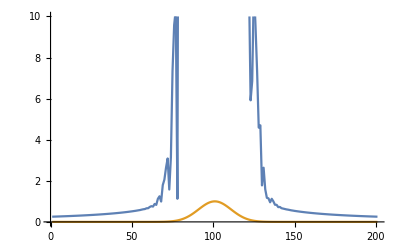

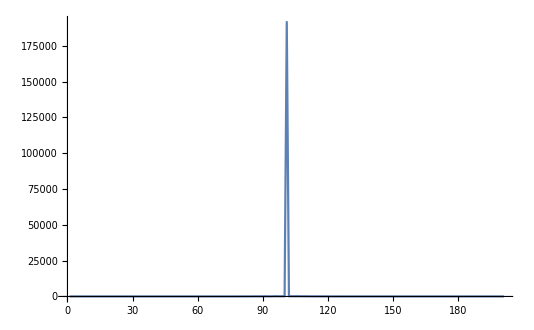

```mathematica
ListPlot[{xaxis,yaxis},Joined->True,PlotRange->{0,10}]
```

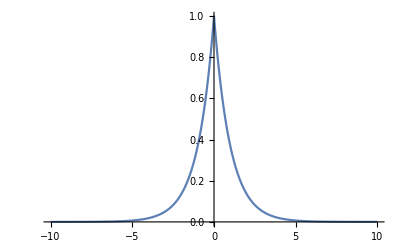

```mathematica
Plot[Exp[-Abs[x]],{x,-10,10},PlotRange->All]
```

```mathematica
Table[NIntegrate[Exp[-Abs[x]]/(Abs[x-y]),{x,-10,10}],{y,-10,10,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-9.9999999999999999999999999998369273566250875478177431028823852055}. NIntegrate obtained 0.211368 and 0.001056 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-9.8999999999999803711709180666198662713034590131993403967249067765}. NIntegrate obtained 0.208868 and 0.00036482 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-9.7999999999999821554486687208371694180097744190081547708149473097}. NIntegrate obtained 0.211269 and 0.00038757 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{0.211368,0.208868,0.211269,0.214415,0.218984,0.227606,0.221831,0.224601,0.231356,0.233679,0.247924,0.237094,0.240345,0.248774,0.260692,0.274416,0.255514,0.259407,0.271039,0.279052,0.311,0.2784,0.29605,0.27098,0.310991,0.363075,0.307802,0.334113,0.311689,0.354888,0.439662,0.346983,0.386333,0.356169,0.416908,0.555429,0.392406,0.470707,0.653107,0.507112,0.734298,0.464829,0.586703,0.502072,0.641642,1.01537,0.570759,0.761622,1.25826,0.846402,1.46269,0.730025,1.02919,1.10045,1.16292,2.18125,1.47292,1.4415,2.81034,1.65766,3.93265,2.17255,2.075,2.33823,1.35116,6.20378,3.30014,3.02355,14.5115,4.30734,17.6132,3.78487,4.2823,6.70452,14.5262,15.9932,8.1184,3.97939,17.811,10.8418,21.6099,20.329,14.7418,16.5217,31.8895,35.163,38.7787,19.0119,47.184,24.6058,57.4422,53.1736,34.6328,37.7642,85.271,94.1597,103.999,56.4321,127.029,60.4995,191613.,118.965,115.204,94.7546,103.999,94.1597,85.271,66.0702,69.9672,53.1736,57.4422,45.0313,43.4195,35.9694,38.7787,35.163,31.8895,25.1779,26.2414,20.329,21.6099,17.362,13.6844,15.0661,31.6397,15.9932,14.5262,11.1479,11.9936,7.92513,17.6132,7.08875,5.41808,5.90689,3.15751,6.20378,5.65648,4.21016,4.71047,2.10578,3.93265,2.20871,2.35057,2.27797,0.975079,2.18125,2.00882,1.50779,1.70979,0.730025,1.46269,1.1834,1.11006,1.06201,0.570759,1.01537,0.948373,0.798299,0.831572,0.464829,0.734298,0.637156,0.653107,0.579565,0.539971,0.555429,0.528166,0.356169,0.386333,0.434222,0.439662,0.405058,0.311689,0.334113,0.362215,0.363075,0.351052,0.27098,0.29605,0.312902,0.311,0.292714,0.271039,0.259407,0.268891,0.274416,0.268424,0.244037,0.240345,0.248793,0.247924,0.240496,0.239181,0.224601,0.229187,0.227606,0.22413,0.218179,0.211269,0.213559,0.211368}

```mathematica
Integrate[x^-2*(Sin[x])^2,{x,-10,10}]
```

```mathematica
Table[Integrate[(x-y)^-2*(Sin[x])^2,{x,-10,10}],{y,-10,10,0.1}]
```

Integrate::idiv: Integral of Sin[x]^2/(10.  + x)^2 does not converge on {-10, 10}.

Integrate::idiv: Integral of Sin[x]^2/(9.9  + x)^2 does not converge on {-10, 10}.

Integrate::idiv: Integral of Sin[x]^2/(9.8  + x)^2 does not converge on {-10, 10}.

General::stop: Further output of Integrate :: idiv will be suppressed during this calculation.

$Aborted

```mathematica
Gaussian[x_]=Exp[-x^2/2]
```

ⅇ^(-x^2/2)

```mathematica
Hartree[x_,y_] = Gaussian[x]/Abs[x-y]
```

(ⅇ^(-x^2/2))/Abs[x-y]

```mathematica
NIntegrate[Hartree[x,1],{x,-10,0.9}] + NIntegrate[Hartree[x,1],{x,1.1,10}]
```

3.58618

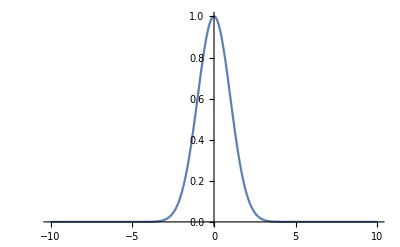

```mathematica
Plot[Gaussian[x],{x,-10,10}, PlotRange->All]
```

```mathematica
Hart=Table[NIntegrate[Hartree[x,y],{x,-10,y-0.1}] + NIntegrate[Hartree[x,y],{x,y+0.1,10}],{y,-9.8,9.8,0.1}]
```

{0.25853,0.261254,0.264038,0.266882,0.269789,0.272761,0.2758,0.278908,0.282089,0.285343,0.288675,0.292087,0.295581,0.299162,0.302831,0.306594,0.310452,0.314411,0.318474,0.322645,0.326929,0.331331,0.335856,0.340508,0.345294,0.350219,0.355291,0.360515,0.365899,0.37145,0.377178,0.383089,0.389195,0.395504,0.402028,0.408778,0.415766,0.423007,0.430514,0.438303,0.446391,0.454797,0.463541,0.472644,0.482132,0.492031,0.50237,0.513181,0.524502,0.536372,0.548837,0.561948,0.575765,0.590352,0.605787,0.622157,0.639562,0.65812,0.677966,0.699258,0.722179,0.746943,0.773796,0.803023,0.834952,0.869957,0.908461,0.950941,0.997925,1.04999,1.10777,1.17192,1.24313,1.3221,1.40952,1.50604,1.61223,1.72856,1.85535,1.99274,2.14061,2.2986,2.46601,2.64183,2.82467,3.01279,3.20408,3.39612,3.58618,3.7713,3.94838,4.11423,4.26571,4.3998,4.51372,4.60505,4.67179,4.71244,4.7261,4.71244,4.67179,4.60505,4.51372,4.3998,4.26571,4.11423,3.94838,3.7713,3.58618,3.39612,3.20408,3.01279,2.82467,2.64183,2.46601,2.2986,2.14061,1.99274,1.85535,1.72856,1.61223,1.50604,1.40952,1.3221,1.24313,1.17192,1.10777,1.04999,0.997925,0.950941,0.908461,0.869957,0.834952,0.803023,0.773796,0.746943,0.722179,0.699258,0.677966,0.65812,0.639562,0.622157,0.605787,0.590352,0.575765,0.561948,0.548837,0.536372,0.524502,0.513181,0.50237,0.492031,0.482132,0.472644,0.463541,0.454797,0.446391,0.438303,0.430514,0.423007,0.415766,0.408778,0.402028,0.395504,0.389195,0.383089,0.377178,0.37145,0.365899,0.360515,0.355291,0.350219,0.345294,0.340508,0.335856,0.331331,0.326929,0.322645,0.318474,0.314411,0.310452,0.306594,0.302831,0.299162,0.295581,0.292087,0.288675,0.285343,0.282089,0.278908,0.2758,0.272761,0.269789,0.266882,0.264038,0.261254,0.25853}

```mathematica
Gauss = Table[Gaussian[x],{x,-10,10,0.1}]
```

{1.92875×10^-22,5.21674×10^-22,1.39694×10^-21,3.70353×10^-21,9.72099×10^-21,2.52616×10^-20,6.49935×10^-20,1.65552×10^-19,4.17501×10^-19,1.04241×10^-18,2.57676×10^-18,6.30619×10^-18,1.52798×10^-17,3.66543×10^-17,8.70543×10^-17,2.04697×10^-16,4.7653×10^-16,1.09831×10^-15,2.50622×10^-15,5.662×10^-15,1.26642×10^-14,2.8044×10^-14,6.1484×10^-14,1.33457×10^-13,2.86798×10^-13,6.10194×10^-13,1.28534×10^-12,2.68055×10^-12,5.53461×10^-12,1.13138×10^-11,2.28973×10^-11,4.58796×10^-11,9.10147×10^-11,1.78756×10^-10,3.47589×10^-10,6.69159×10^-10,1.27541×10^-9,2.40672×10^-9,4.49635×10^-9,8.3167×10^-9,1.523×10^-8,2.76124×10^-8,4.95641×10^-8,8.80818×10^-8,1.54975×10^-7,2.69958×10^-7,4.65572×10^-7,7.94939×10^-7,1.34381×10^-6,2.24906×10^-6,3.72665×10^-6,6.11357×10^-6,9.9295×10^-6,0.0000159668,0.0000254193,0.0000400653,0.0000625215,0.0000965934,0.000147748,0.000223746,0.000335463,0.000497955,0.000731802,0.00106477,0.00153381,0.00218749,0.00308872,0.00431784,0.00597602,0.0081887,0.011109,0.0149208,0.0198411,0.0261214,0.0340475,0.0439369,0.0561348,0.0710054,0.0889216,0.110251,0.135335,0.164474,0.197899,0.235746,0.278037,0.324652,0.375311,0.429557,0.486752,0.546074,0.606531,0.666977,0.726149,0.782705,0.83527,0.882497,0.923116,0.955997,0.980199,0.995012,1.,0.995012,0.980199,0.955997,0.923116,0.882497,0.83527,0.782705,0.726149,0.666977,0.606531,0.546074,0.486752,0.429557,0.375311,0.324652,0.278037,0.235746,0.197899,0.164474,0.135335,0.110251,0.0889216,0.0710054,0.0561348,0.0439369,0.0340475,0.0261214,0.0198411,0.0149208,0.011109,0.0081887,0.00597602,0.00431784,0.00308872,0.00218749,0.00153381,0.00106477,0.000731802,0.000497955,0.000335463,0.000223746,0.000147748,0.0000965934,0.0000625215,0.0000400653,0.0000254193,0.0000159668,9.9295×10^-6,6.11357×10^-6,3.72665×10^-6,2.24906×10^-6,1.34381×10^-6,7.94939×10^-7,4.65572×10^-7,2.69958×10^-7,1.54975×10^-7,8.80818×10^-8,4.95641×10^-8,2.76124×10^-8,1.523×10^-8,8.3167×10^-9,4.49635×10^-9,2.40672×10^-9,1.27541×10^-9,6.69159×10^-10,3.47589×10^-10,1.78756×10^-10,9.10147×10^-11,4.58796×10^-11,2.28973×10^-11,1.13138×10^-11,5.53461×10^-12,2.68055×10^-12,1.28534×10^-12,6.10194×10^-13,2.86798×10^-13,1.33457×10^-13,6.1484×10^-14,2.8044×10^-14,1.26642×10^-14,5.662×10^-15,2.50622×10^-15,1.09831×10^-15,4.7653×10^-16,2.04697×10^-16,8.70543×10^-17,3.66543×10^-17,1.52798×10^-17,6.30619×10^-18,2.57676×10^-18,1.04241×10^-18,4.17501×10^-19,1.65552×10^-19,6.49935×10^-20,2.52616×10^-20,9.72099×10^-21,3.70353×10^-21,1.39694×10^-21,5.21674×10^-22,1.92875×10^-22}

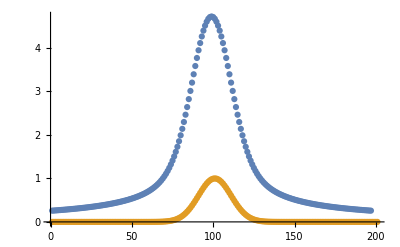

```mathematica
ListPlot[{Hart,Gauss},PlotRange->All]
```

```mathematica
Plot[0.8Gaussian[x] + 0.1*Gaussian[x+5] + 0.1*Gaussian[x-5],{x,-10,10},PlotRange->All]
```

```mathematica
Hartree2[x_,y_]=(0.8Gaussian[x] + 0.1*Gaussian[x+5] + 0.1*Gaussian[x-5])/Abs[x-y]
```

(0.1 ⅇ^(-1/2 (-5+x)^2)+0.8 ⅇ^(-x^2/2)+0.1 ⅇ^(-1/2 (5+x)^2))/Abs[x-y]

```mathematica
Hart=Table[NIntegrate[Hartree2[x,y],{x,-10,y-0.1}] + NIntegrate[Hartree2[x,y],{x,y+0.1,10}],{y,-9.8,9.8,0.1}]
```

{0.278722,0.28233,0.286057,0.289911,0.293902,0.29804,0.302337,0.306807,0.311465,0.316328,0.321419,0.326759,0.332377,0.338303,0.344572,0.351226,0.358308,0.365871,0.37397,0.382666,0.392025,0.402118,0.413019,0.4248,0.437536,0.451296,0.466143,0.482129,0.499291,0.51765,0.537202,0.557915,0.57973,0.602551,0.62625,0.650661,0.675584,0.700787,0.726009,0.750967,0.775364,0.798897,0.821267,0.84219,0.861409,0.878702,0.893893,0.906858,0.917536,0.925928,0.932101,0.936189,0.938388,0.93895,0.938179,0.936424,0.934067,0.931517,0.929199,0.927553,0.927019,0.928042,0.931062,0.936517,0.944846,0.956484,0.971875,0.991467,1.01572,1.04511,1.08013,1.12127,1.16904,1.22394,1.28646,1.35705,1.43609,1.5239,1.62067,1.72643,1.84105,1.96418,2.09522,2.23331,2.37732,2.5258,2.67706,2.82912,2.97979,3.12668,3.2673,3.39908,3.5195,3.62614,3.71677,3.78944,3.84255,3.87491,3.88578,3.87491,3.84255,3.78944,3.71677,3.62614,3.5195,3.39908,3.2673,3.12668,2.97979,2.82912,2.67706,2.5258,2.37732,2.23331,2.09522,1.96418,1.84105,1.72643,1.62067,1.5239,1.43609,1.35705,1.28646,1.22394,1.16904,1.12127,1.08013,1.04511,1.01572,0.991467,0.971875,0.956484,0.944846,0.936517,0.931062,0.928042,0.927019,0.927553,0.929199,0.931517,0.934067,0.936424,0.938179,0.93895,0.938388,0.936189,0.932101,0.925928,0.917536,0.906858,0.893893,0.878702,0.861409,0.84219,0.821267,0.798897,0.775364,0.750967,0.726009,0.700787,0.675584,0.650661,0.62625,0.602551,0.57973,0.557915,0.537202,0.51765,0.499291,0.482129,0.466143,0.451296,0.437536,0.4248,0.413019,0.402118,0.392025,0.382666,0.37397,0.365871,0.358308,0.351226,0.344572,0.338303,0.332377,0.326759,0.321419,0.316328,0.311465,0.306807,0.302337,0.29804,0.293902,0.289911,0.286057,0.28233,0.278722}

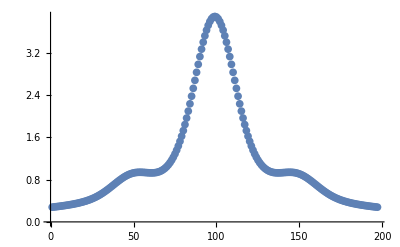

```mathematica
ListPlot[Hart]
```

```mathematica
matrix = {{0.1,0.2,0.3},{0.2,0.5,0.1},{2,0.2,0.1}}
```

{{0.1,0.2,0.3},{0.2,0.5,0.1},{2,0.2,0.1}}

```mathematica
Eigenvalues[matrix]
```

{0.968204,-0.632406,0.364202}

```mathematica
diagonalmat = DiagonalMatrix[Eigenvalues[matrix]] // MatrixForm
```

(1.00095 | 0. | 0.
0. | -0.671442 | 0.
0. | 0. | 0.370492)

```mathematica
MatrixPower[matrix,1000]
```

{{1.05773,0.589004,0.41758},{0.932318,0.519168,0.368069},{2.55499,1.42277,1.00868}}